```mathematica
Quit[]
```

## Grand Hatsuda-Okazaki

Follow 2208.01426 (4.2)

### Test θ derivative formula (3.10)

```mathematica
tmp=ⅈ q^(-1/8) D[EllipticTheta[1,Log[u]/(2ⅈ),Sqrt[q]],u]/.u->1
```

EllipticThetaPrime[1,0,√q]/(2 q^(1/8))

```mathematica
tmp/(q^(-1/8)DedekindEta[Log[q]/(2π ⅈ)]^3)/.q->Exp[-π]//N
```

1.

```mathematica
Series[tmp^(1/3),{q,0,5}]
```

1-q-q^2+q^5+O[q]^(41/8)

```mathematica
Series[q^(-1/24)DedekindEta[Log[q]/(2π ⅈ)],{q,0,5}]
```

1-q-q^2+q^5+O[q]^(121/24)

### Grand u=1

```mathematica
cut=4;
NN=2;
(*θ[u_,q_]:=Series[ⅈ q^(-1/8)EllipticTheta[1,Log[u]/(2ⅈ),Sqrt[q]],{q,0,2cut+2}];*)
θ[u_,q_]:=-u^(-1/2)QPochhammer[q,q]QPochhammer[u,q]QPochhammer[q u^-1,q];
Λ[N_,b_,q_]:=(-1)^N ξ^(N^2/2)(q^(-1/8)DedekindEta[Log[q]/(2π ⅈ)]^3)/θ[ξ^-N,q]/.ξ->q^(-1/2)b(*//TrigToExp*);
Λq[N_,b_,q_]:=Series[Λ[N,b,q],{q,0,cut}];
```

```mathematica
tmp1=Simplify[Λq[NN,b,q],Assumptions->{b>0,q>0}];
```

```mathematica
Ξ[μ_,b_,q_]:=μ Product[1-μ ξ^-p/(1-q^p),{p,1,2cut}]Product[1-μ ξ^-p/(1-q^p),{p,-2cut,-1}]/.ξ->q^(-1/2)b;
```

```mathematica
tmp2=1+Series[SeriesCoefficient[Ξ[μ,b,q],{μ,0,NN}],{q,0,cut}];
```

```mathematica
Series[Normal[Series[(-x(1-b^2)/b)tmp1*tmp2,{q,0,cut}]]/.q->x^2//PowerExpand,{x,0,2cut},{b,0,10}]
```

1+(-1/b+b+O[b]^11) x+(-2+2 b^2+O[b]^11) x^2+(-2/b^3+2/b-2 b+2 b^3+O[b]^11) x^3+(-1/b^4+1/b^2-3 b^2+3 b^4+O[b]^11) x^4+(-3/b^5+3/b^3-3 b^3+3 b^5+O[b]^11) x^5+(-2/b^6+2/b^4-2/b^2+2-4 b^4+4 b^6+O[b]^11) x^6+(-4/b^7+4/b^5-4 b^5+4 b^7+O[b]^11) x^7+(-3/b^8+3/b^6-5 b^6+5 b^8+O[b]^11) x^8+O[x]^9

```mathematica
-x^2 Series[Normal[Series[tmp1*tmp2,{q,0,cut}]]/.q->x^2//PowerExpand,{x,0,2cut},{b,0,10}]
```

(b+b^3+b^5+b^7+b^9+O[b]^11) x-x^2+(-2 b+O[b]^11) x^3+(-2/b^2-2 b^2+O[b]^11) x^4+(-1/b^3-3 b^3+O[b]^11) x^5+(-3/b^4-3 b^4+O[b]^11) x^6+(-2/b^5-2/b-4 b^5+O[b]^11) x^7+(-4/b^6-4 b^6+O[b]^11) x^8+(-3/b^7-5 b^7+O[b]^11) x^9+O[x]^11

### GAP

```mathematica
n=12;
tmp=Series[1+Sum[indexGAP[3,i],{i,1,n}],{x,0,n}]//Simplify
```

1+(1/b+b) x+(2 (1+b^4) x^2)/b^2+(3/b^3+1/b+b+3 b^3) x^3+(1+4/b^4+4 b^4) x^4+(5/b^5+1/b^3+1/b+b+b^3+5 b^5) x^5+(2+7/b^6+2/b^2+2 b^2+7 b^6) x^6+(8/b^7+1/b^5+1/b^3+2/b+2 b+b^3+b^5+8 b^7) x^7+(2 (5+b^4+b^6+b^8+b^10+b^12+5 b^16) x^8)/b^8+(12/b^9+1/b^7+1/b^5+1/b^3+2/b+2 b+b^3+b^5+b^7+12 b^9) x^9+(2 (7+b^4+b^6+2 b^8+b^10+2 b^12+b^14+b^16+7 b^20) x^10)/b^10+(16/b^11+1/b^9+1/b^7+2/b^5+3/b^3+3/b+3 b+3 b^3+2 b^5+b^7+b^9+16 b^11) x^11+(6+19/b^12+2/b^8+2/b^6+4/b^4+4 b^4+2 b^6+2 b^8+19 b^12) x^12+O[x]^13

```mathematica
n=12;
tmp=Series[1+Sum[indexGAP[2,i],{i,1,n}],{x,0,n}]//Simplify
```

1+(1/b+b) x+(2 (1+b^4) x^2)/b^2+(2 (1+b^6) x^3)/b^3+(3 (1+b^8) x^4)/b^4+(3/b^5+1/b+b+3 b^5) x^5+(4 (1+b^12) x^6)/b^6+(4 (1+b^14) x^7)/b^7+(3+5/b^8+5 b^8) x^8+(5/b^9+1/b^3+b^3+5 b^9) x^9+(6 (1+b^20) x^10)/b^10+(2 (3+b^10+b^12+3 b^22) x^11)/b^11+(7 (1+b^24) x^12)/b^12+O[x]^13

```mathematica
n=12;
tmp=Series[1+Sum[indexGAP[1,i],{i,1,n}],{x,0,n}]//Simplify
```

1+(1/b+b) x+(-1+1/b^2+b^2) x^2+(1/b^3+b^3) x^3+(1/b^4+b^4) x^4+(1/b^5-1/b-b+b^5) x^5+(1+1/b^6+b^6) x^6+(1/b^7+b^7) x^7+(1/b^8-1/b^2-b^2+b^8) x^8+(1/b^9+b^9) x^9+(1/b^10+b^10) x^10+(1/b^11-1/b^3+1/b+b-b^3+b^11) x^11+(-1+1/b^12+b^12) x^12+O[x]^13

### Grand u=1

```mathematica
S[expr_]:=Simplify[expr,Assumptions->{u>0,ξ>0,b>0,q>0}];
```

```mathematica
cut=4;
NN=1;
θ[u_,q_]:=-u^(-1/2)QPochhammer[q,q]QPochhammer[u,q]QPochhammer[q u^-1,q];
Λ[N_,b_,q_]:=(-1)^N ξ^(N^2/2)QPochhammer[q,q]^3/θ[ξ^-N,q](*(q^(-1/8)DedekindEta[Log[q]/(2π ⅈ)]^3)*);
(*Λq[N_,b_,q_]:=Series[Λ[N,b,q],{q,0,cut}];*)
Series[Λ[NN,q^-1ξ^-1,q]/((-1)^(-NN )Λ[NN,ξ,q]),{q,0,cut}]//PowerExpand
```

-1

```mathematica
(*Ξ[μ_,ξ_,q_]:=μ Product[1-μ ξ^-p/(1-q^p),{p,1,4Max[cut,Ceiling[1/4 NN √(1+8 cut)]]}]*Product[1-μ ξ^-p/(1-q^p),{p,-4Max[cut,Ceiling[1/4 NN √(1+8 cut)]],-1}];*)
Ξ[μ_,ξ_,q_]:=μ Product[(1-μ ξ^-p/(1-q^p))(1+μ ξ^p q^p/(1-q^p)),{p,1,4Max[cut,Ceiling[1/4 NN √(1+8 cut)]]}];
```

```mathematica
Series[Ξ[μ,ξ,q]/Ξ[-μ,ξ^-1q^-1,q],{q,0,cut}]
```

-1

```mathematica
Z[N_,ξ_,q_]:=SeriesCoefficient[Ξ[μ,ξ,q],{μ,0,N}];
Series[(-1)^NN Z[NN,ξ,q]/Z[NN,ξ^-1q^-1,q],{q,0,cut}]//S
```

-1

```mathematica
II[N_,ξ_,q_]:=Λ[N,ξ,q]Z[N,ξ,q];
```

```mathematica
Series[II[NN,ξ,q]/.ξ->q^(-1/2)b/.q->x^2,{x,0,2cut}]//S//PowerExpand//Simplify
```

1+(1/b+b) x+(-1+1/b^2+b^2) x^2+(1/b^3+b^3) x^3+(1/b^4+b^4) x^4+(1/b^5-1/b-b+b^5) x^5+(1+1/b^6+b^6) x^6+(1/b^7+b^7) x^7+(1/b^8-1/b^2-b^2+b^8) x^8+O[x]^9

```mathematica
U[μ_,ξ_,q_]:=μ Product[(1+μ ξ^-p/(1-q^p))(1+μ ξ^p q^p/(1-q^p)),{p,1,4Max[cut,Ceiling[1/4 NN √(1+8 cut)]]}];
```

```mathematica
Series[U[NN,ξ,q]/.ξ->q^(-1/2)b/.b->1/.q->x^2,{x,0,2cut}]//S//PowerExpand//Simplify
```

1+2 x+3 x^2+8 x^3+11 x^4+20 x^5+35 x^6+52 x^7+82 x^8+O[x]^9

```mathematica
ans1=Series[II[NN,ξ,q]/.ξ->q^(-1/2)b/.q->x^2,{x,0,2cut}]//S//PowerExpand//Simplify
```

1+(1/b+b) x+(-1+1/b^2+b^2) x^2+(1/b^3+b^3) x^3+(1/b^4+b^4) x^4+(1/b^5-1/b-b+b^5) x^5+(1+1/b^6+b^6) x^6+(1/b^7+b^7) x^7+(1/b^8-1/b^2-b^2+b^8) x^8+O[x]^9

```mathematica
ans2/ans1//S
```

1+(1+1/b^2+b^2) x^2-(2 (1+b^2) x^3)/b+((1+b^2+b^4)^2 x^4)/b^4-(2 (1+2 b^2+2 b^4+b^6) x^5)/b^3+(6+1/b^6+2/b^4+5/b^2+5 b^2+2 b^4+b^6) x^6-(2 ((1+b^2) (1+b^2+b^4)^2) x^7)/b^5+((1+b^2)^2 (1+5 b^4+3 b^6+5 b^8+b^12) x^8)/b^8+O[x]^9

### Grand general u

```mathematica
S[expr_]:=Simplify[expr,Assumptions->{u>0,ξ>0,b>0,q>0}];
```

```mathematica
cut=4;
NN=2;
```

```mathematica
Λ[N_,u_,ξ_,q_]:=(-1)^N ξ^(N^2/2)θ[u,q]/θ[u ξ^(-N),q];
Series[(-1)^(NN+1)ξ^(-NN^2/2)Λ[NN,ξ^(NN/2),ξ,q],{q,0,cut}]//PowerExpand
Series[Λ[NN,u^-1,q^-1ξ^-1,q]/((-u)^(-NN )Λ[NN,u,ξ,q]),{q,0,cut}]//PowerExpand
```

1+O[q]^5

1+O[q]^5

```mathematica
Λ[NN,u^-1,q^-1ξ^-1,q]/((-u)^(-NN )Λ[NN,u,ξ,q])/.{u->Exp[-π/2],ξ->Exp[-2π],q->Exp[-π]}//N
```

1.

```mathematica
(* Range: see (3.4) *)
Ξ[μ_,u_,ξ_,q_]:=Product[1-μ ξ^-p/(1-u q^p),{p,-2Max[cut,Ceiling[1/4 NN √(1+8 cut)]],2Max[cut,Ceiling[1/4 NN √(1+8 cut)]]}];
Series[Ξ[μ,u,ξ,q]/Ξ[-u^-1μ,u^-1,ξ^-1q^-1,q],{q,0,cut}]
```

1+O[q]^5

```mathematica
Z[N_,u_,ξ_,q_]:=SeriesCoefficient[Ξ[μ,u,ξ,q],{μ,0,N}];
Series[(-u)^NN Z[NN,u,ξ,q]/Z[NN,u^-1,ξ^-1q^-1,q],{q,0,cut}]//S
```

1+O[q]^5

```mathematica
II[N_,u_,ξ_,q_]:=Λ[N,u,ξ,q]Z[N,u,ξ,q];
```

```mathematica
Series[II[NN,u,ξ,q]/.u->ξ^(NN/2)/.ξ->q^(-1/2)b/.q->x^2,{x,0,2cut}]//S//PowerExpand//Simplify
```

1+(1/b+b) x+(2 (1+b^4) x^2)/b^2+(2 (1+b^6) x^3)/b^3+(3 (1+b^8) x^4)/b^4+(3/b^5+1/b+b+3 b^5) x^5+(4 (1+b^12) x^6)/b^6+(4 (1+b^14) x^7)/b^7+(3+5/b^8+5 b^8) x^8+O[x]^10

```mathematica
Series[II[NN,u,ξ,q]/.u->-1/.ξ->q^(-1/2)b/.q->x^2,{x,0,2cut}]//S//PowerExpand//Simplify
```

1+(1/b+b) x+(2 (1+b^4) x^2)/b^2+(2 (1+b^6) x^3)/b^3+(3 (1+b^8) x^4)/b^4+(3/b^5+1/b+b+3 b^5) x^5+(4 (1+b^12) x^6)/b^6+(4 (1+b^14) x^7)/b^7+(2+4/b^8+1/b^6-1/b^4+1/b^2+b^2-b^4+b^6+4 b^8) x^8+O[x]^9

```mathematica
Series[II[NN,u,ξ,q]/.u->1/2/.ξ->q^(-1/2)b/.q->x^2,{x,0,2cut}]//S//PowerExpand//Simplify
```

1+(1/b+b) x+(2 (1+b^4) x^2)/b^2+(2 (1+b^6) x^3)/b^3+(3 (1+b^8) x^4)/b^4+(3/b^5+1/b+b+3 b^5) x^5+(4 (1+b^12) x^6)/b^6+(4 (1+b^14) x^7)/b^7+((4-10 b^2+3 b^8-6 b^10+5 b^16-8 b^18) x^8)/(b^8-2 b^10)+O[x]^9

```mathematica
Series[II[NN,u,ξ,q]/.ξ->q^(-1/2)b/.q->x^2,{x,0,2cut}]//S//PowerExpand//Simplify
```

1+(1/b+b) x+(2 (1+b^4) x^2)/b^2+(2 (1+b^6) x^3)/b^3+(3 (1+b^8) x^4)/b^4+(3/b^5+1/b+b+3 b^5) x^5+(4 (1+b^12) x^6)/b^6+(4 (1+b^14) x^7)/b^7+((5 b^2+3 b^10+4 b^18-4 u-3 b^8 u-5 b^16 u) x^8)/(b^10-b^8 u)+O[x]^9

```mathematica
Series[Z[NN,u,ξ,q]/.u->ξ^(NN/2),{q,0,cut}]
```

(-1-ξ^2-ξ^4-ξ^6-ξ^8-ξ^10-ξ^12-ξ^14)/((-1+ξ) ξ^15)-q/ξ+((-1-2 ξ^3) q^2)/ξ^3+((-1-ξ^4-2 ξ^6) q^3)/ξ^5+((-1-3 ξ^5-3 ξ^9) q^4)/ξ^7+O[q]^5

```mathematica
Series[(-1)^(NN+1)ξ^(NN^2/2)Z[NN,u,ξ,q]/.u->ξ^(NN/2)/.ξ->q^(-1/2)b/.q->x^2,{x,0,2cut}]//S//PowerExpand//Simplify
```

1+(1/b+b) x+(2 (1+b^4) x^2)/b^2+(2 (1+b^6) x^3)/b^3+(3 (1+b^8) x^4)/b^4+(3/b^5+1/b+b+3 b^5) x^5+(4 (1+b^12) x^6)/b^6+(4 (1+b^14) x^7)/b^7+(3+5/b^8+5 b^8) x^8+O[x]^9

```mathematica
n=2cut;
tmp=Series[1+Sum[indexGAP[2,i],{i,1,n}],{x,0,n}]//Simplify
```

1+(1/b+b) x+(2 (1+b^4) x^2)/b^2+(2 (1+b^6) x^3)/b^3+(3 (1+b^8) x^4)/b^4+(3/b^5+1/b+b+3 b^5) x^5+(4 (1+b^12) x^6)/b^6+(4 (1+b^14) x^7)/b^7+(3+5/b^8+5 b^8) x^8+O[x]^9

### Grand general u

```mathematica
cut=10;
NN=2;
Ξ[μ_,u_,ξ_,q_]:=Product[1-μ ξ^-p/(1-u q^p),{p,-cut,cut}];
```

```mathematica
(*θ[u_,q_]:=Series[ⅈ q^(-1/8)EllipticTheta[1,Log[u]/(2ⅈ),Sqrt[q]],{q,0,2cut+2}];*)
θ[u_,q_]:=-u^(-1/2)QPochhammer[q,q]QPochhammer[u,q]QPochhammer[q u^-1,q];
Λ[N_,u_,b_,q_]:=(-1)^N ξ^(N^2/2)θ[u,q]/θ[u ξ^(-N),q]/.ξ->q^(-1/2)b(*//TrigToExp*);
Λq[N_,u_,b_,q_]:=S[Series[Λ[N,u,b,q],{q,0,cut}]];
Ξ[μ_,u_,b_,q_]:=Product[1-μ ξ^-p/(1-u q^p),{p,-2cut,2cut}]/.ξ->q^(-1/2)b;
Z[N_,u_,b_,q_]:=SeriesCoefficient[Ξ[μ,u,ξ,q],{μ,0,N}];
(*II[N_,u_,b_,q_]:=Λq[N,u,b,q]SeriesCoefficient[Ξ[μ,u,b,q],{μ,0,N}];*)
```

```mathematica
tmp1=Λq[NN,u,b,q];
tmp2=1+Series[SeriesCoefficient[Ξ[μ,u,b,q],{μ,0,NN}],{q,0,cut}];
```

```mathematica
tmp1*tmp2//S
```

u+(b (2-1/u)+(1-u+u^2)/b) √q+((u^2-u^4+u^5+b^4 (-1+u+u^2)-b^2 u (-1+3 u-2 u^2+u^3)) q)/(b^2 u^2)+((-b^4 (-1+u)^3 u+u^3-b^2 (-1+u)^3 u^3-u^6+u^7+b^6 (-1+u+u^3)) q^(3/2))/(b^3 u^3)+((-b^6 (-1+u)^3 u-2 b^4 (-1+u)^3 u^3+u^4-b^2 (-1+u)^3 u^5-u^8+u^9+b^8 (-1+u+u^4)) q^2)/(b^4 u^4)+(b (7+3/u^2-8/u-3 u)-(b^3 (-1+u)^3)/u^4-((-1+u)^3 u^2)/b^3+(2-8 u+8 u^2-3 u^3)/b+(b^5 (-1+u+u^5))/u^5+(1-u^5+u^6)/b^5) q^(5/2)+(-13-(b^4 (-1+u)^3)/u^5-(3 b^2 (-1+u)^3)/u^3-1/u^2+6/u+14 u-(3 (-1+u)^3 u)/b^2-6 u^2+u^3-((-1+u)^3 u^3)/b^4+(b^6 (-1+u+u^6))/u^6+(1-u^6+u^7)/b^6) q^3+O[q]^(13/4)

### Grand old

```mathematica
cut=2;
θ[u_,q_]:=Series[ⅈ q^(-1/8)EllipticTheta[1,Log[u]/(2ⅈ),Sqrt[q]],{q,0,cut+2}];
ξ^(1/2)*(q^(-1/8)DedekindEta[Log[q]/(2π ⅈ)]^3)/θ[ξ,q]//TrigToExp//Simplify
```

ξ/(-1+ξ)+(-1+ξ) q+((-1+ξ^3) q^2)/ξ+O[q]^3

```mathematica
cut=2;
(*θ[u_,q_]:=Series[ⅈ q^(-1/8)EllipticTheta[1,Log[u]/(2ⅈ),Sqrt[q]],{q,0,cut+2}];*)
θ[u_,q_]:=ⅈ q^(-1/8)EllipticTheta[1,Log[u]/(2ⅈ),Sqrt[q]];
Λ[N_,u_,ξ_,q_]:=(-1)^N ξ^(N^2/2)θ[u,q]/θ[u ξ^-N,q];
(*Ξ[μ_,u_,ξ_,q_]:=(1-μ/(1-u))Product[(1-μ ξ^-p/(1-u q^p))(1+μ u^-1 ξ^p q^p/(1-u^-1q^p)),{p,1,cut}];*)
Ξ[μ_,u_,ξ_,q_]:=Product[1-μ ξ^-p/(1-u q^p),{p,-cut,cut}];
II[N_,u_,ξ_,q_]:=Λ[N,u,ξ,q]SeriesCoefficient[Ξ[μ,u,ξ,q],{μ,0,N}]//Simplify;
```

```mathematica
tmp=Series[II[1,u,ξ,q]/.{ξ->q^(-1/2)t^2},{q,0,cut}];
```

$Aborted

```mathematica
Series[Simplify[Limit[tmp,u->1]//TrigToExp,Assumptions->ξ>0],{q,0,cut}]//Simplify
```

ξ/(-1+ξ)+(-1+ξ) q+((-1+ξ^3) q^2)/ξ+O[q]^3

```mathematica
Series[Simplify[Limit[tmp,u->1]//TrigToExp,Assumptions->ξ>0],{q,0,cut}]//Simplify
```

ξ/(-1+ξ)+(-1+ξ) q+((-1+ξ^3) q^2)/ξ+(1-1/ξ^2-ξ+ξ^3) q^3+O[q]^4

```mathematica
Series[Simplify[Limit[tmp,u->1]//TrigToExp,Assumptions->ξ>0],{q,0,cut}]//Simplify
```

ξ/(-1+ξ)+(-1+ξ) q+((-1+ξ^3) q^2)/ξ+(1-1/ξ^2-ξ+ξ^3) q^3+((-1+ξ^7) q^4)/ξ^3+O[q]^5

```mathematica
Series[Simplify[Limit[tmp,u->1]//TrigToExp,Assumptions->ξ>0],{q,0,cut}]//Simplify
```

ξ/(-1+ξ)+(-1-1/ξ+ξ) q-((1+ξ+ξ^3+ξ^4-ξ^5) q^2)/ξ^3+O[q]^3

```mathematica
Series[Simplify[Limit[tmp,u->1]//TrigToExp,Assumptions->ξ>0],{q,0,cut}]//Simplify
```

(1+ξ^2)/((-1+ξ) ξ)+((-1-ξ+ξ^4) q)/ξ^3-((1+ξ+ξ^2+ξ^3+ξ^5-2 ξ^7) q^2)/ξ^5+O[q]^3

```mathematica
Series[Simplify[Limit[tmp,u->1]//TrigToExp,Assumptions->ξ>0],{q,0,cut}]//Simplify
```

(1+ξ^2+ξ^4+ξ^6)/((-1+ξ) ξ^5)+((-1-ξ+ξ^8) q)/ξ^7-((1+ξ+ξ^2+ξ^3+ξ^4+ξ^5-ξ^8-2 ξ^11) q^2)/ξ^9+O[q]^3

```mathematica
Series[Simplify[Limit[tmp,u->1]//TrigToExp,Assumptions->ξ>0],{q,0,cut}]//Simplify
```

(1+ξ+ξ^2)/(-1+ξ^2)+((-1-ξ+ξ^3) q)/ξ^2-((1+ξ+ξ^2+ξ^4+ξ^5-2 ξ^6) q^2)/ξ^4-((1+ξ+ξ^2+ξ^6+ξ^8-ξ^9) q^3)/ξ^6+O[q]^4

```mathematica
Series[Simplify[Limit[tmp,u->1]//TrigToExp,Assumptions->ξ>0],{q,0,cut}]//Simplify
```

(1+ξ^2+ξ^4)/((-1+ξ) ξ^3)+((-1-ξ+ξ^6) q)/ξ^5-((1+ξ+ξ^2+ξ^3+ξ^4+ξ^5-ξ^6-2 ξ^9) q^2)/ξ^7-((1+ξ+ξ^2+ξ^3+ξ^7+ξ^8+ξ^9-ξ^10-2 ξ^12) q^3)/ξ^9+O[q]^4

## Residue method

### Flavored Schur closed form

```mathematica
cut=4;
NN=1;
Series[Sum@@Join[{-Product[b^(-2p[i]+NN^2)/(1-b^NN q^p[i]),{i,1,NN}]},{{p[1],-cut,cut}},Table[{p[i],p[i-1]+1,cut},{i,2,NN}]],{q,0,3}]
```

(-1/b^7-1/b^5-1/b^3-1/b-b/(1-b))+(-1+b^2) q+(-1/b^2+b^4) q^2+(1-1/b^4-b^2+b^6) q^3+O[q]^4

```mathematica
tmp
```

1+(1+1/b^2+b^2) x^2+((-1+b^2)^2 (1+b^2) x^3)/b^3+(2+1/b^4+b^4) x^4+((-1+b^2)^2 (1+b^2)^3 x^5)/b^5+(5+2/b^6-1/b^4-b^4+2 b^6) x^6+(1/b^7+3/b^3-4/b-4 b+3 b^3+b^7) x^7+(8+2/b^8+1/b^6-3/b^4-1/b^2-b^2-3 b^4+b^6+2 b^8) x^8+((-1+b^2)^2 (1+b^2)^3 (2-3 b^2+7 b^4-3 b^6+2 b^8) x^9)/b^9+(16+2/b^10+3/b^6-6/b^4-1/b^2-b^2-6 b^4+3 b^6+2 b^10) x^10+(2/b^11+1/b^9-3/b^7+13/b^3-13/b-13 b+13 b^3-3 b^7+b^9+2 b^11) x^11+(28+3/b^12-1/b^10+7/b^6-13/b^4-6/b^2-6 b^2-13 b^4+7 b^6-b^10+3 b^12) x^12+((-1+b^2)^2 (1+b^2)^3 (2-2 b^2+9 b^4-16 b^6+27 b^8-16 b^10+9 b^12-2 b^14+2 b^16) x^13)/b^13+(51+3/b^14+1/b^12-3/b^10+15/b^6-23/b^4-11/b^2-11 b^2-23 b^4+15 b^6-3 b^10+b^12+3 b^14) x^14+(3/b^15-1/b^13+7/b^9-15/b^7-2/b^5+47/b^3-39/b-39 b+47 b^3-2 b^5-15 b^7+7 b^9-b^13+3 b^15) x^15+(89+3/b^16+3/b^12-7/b^10+30/b^6-44/b^4-23/b^2-23 b^2-44 b^4+30 b^6-7 b^10+3 b^12+3 b^16) x^16+((-1+b^2)^2 (1+b^2)^3 (3-2 b^2+5 b^4-3 b^6+22 b^8-49 b^10+78 b^12-49 b^14+22 b^16-3 b^18+5 b^20-2 b^22+3 b^24) x^17)/b^17+(150+4/b^18-1/b^16+7/b^12-16/b^10-1/b^8+59/b^6-77/b^4-41/b^2-41 b^2-77 b^4+59 b^6-b^8-16 b^10+7 b^12-b^16+4 b^18) x^18+(3/b^19+3/b^15-7/b^13+32/b^9-57/b^7-13/b^5+149/b^3-110/b-110 b+149 b^3-13 b^5-57 b^7+32 b^9-7 b^13+3 b^15+3 b^19) x^19+(248+4/b^20+1/b^18-3/b^16+16/b^12-32/b^10-2/b^8+106/b^6-133/b^4-75/b^2-75 b^2-133 b^4+106 b^6-2 b^8-32 b^10+16 b^12-3 b^16+b^18+4 b^20) x^20+O[x]^21

### 1/16 unrefined index

```mathematica
Clear["Global`*"];

(* product of chracters *)
characterProduct[NN_,a_]:=characterProduct[NN,a]=Product[(Sum[w[i]^n/w[j]^n,{i,1,NN},{j,1,NN}]-1)^a[[n]],{n,1,Length[a]}]

(* generate a vector "a" with Sum[i a[[i]],{i,1,NN}] fixed to be L *)
power[NN_,a_]:=power[NN,a]=2 NN-2+2 Sum[i a[[i]],{i,1,Length[a]}]
aVectors[L_]:=aVectors[L]=Module[{partition,vector},
partition=IntegerPartitions[L];
vector[n_]:=Sum[Table[KroneckerDelta[n[[j]],i],{i,1,L}],{j,1,Length[n]}];
Table[vector[partition[[i]]],{i,1,Length[partition]}]
]


coefficient[a_]:=coefficient[a]=Product[1/a[[i]]!/(i^(a[[i]])),{i,1,Length[a]}]

f[x_]:=1-(1-x^2)^3/(1-x^3)^2

groupIntegrand[NN_,a_]:=groupIntegrand[NN,a]=characterProduct[NN,a](*Product[1/w[i],{i,1,NN-1}]*)(-1)^(NN(NN-1)/2)(*/Product[w[i]^(NN-1),{i,1,NN}]*)Product[(w[i]-w[j])^2,{i,1,NN},{j,1,i-1}]/.w[NN]->1/Product[w[i],{i,1,NN-1}]

Clear[groupIntegrandNumerator,groupIntegral,index]
groupIntegrandNumerator[NN_,a_]:=groupIntegrandNumerator[NN,a]=Numerator[groupIntegrand[NN,a]//Together]

groupIntegral[NN_,a_]:=groupIntegral[NN,a]=1/NN!Coefficient[ groupIntegrandNumerator[NN,a]//Expand,Product[w[i],{i,1,NN-1}]^power[NN,a] ]

index[NN_,L_]:=index[NN,L]=Module[{as},
as=aVectors[L];
Sum[Product[f[x^j]^as[[i,j]],{j,1,L}]groupIntegral[NN,as[[i]]]coefficient[as[[i]]],{i,1,Length[as]}]
]
```

```mathematica
NN=2;
LL=30;
AbsoluteTiming[Sum[index[NN,L],{L,0,LL/2}]+O[x]^(LL+1)]
```

{0.390262,1+6 x^4-6 x^5-7 x^6+18 x^7+6 x^8-36 x^9+6 x^10+84 x^11-80 x^12-132 x^13+309 x^14-18 x^15-567 x^16+516 x^17+613 x^18-1392 x^19-180 x^20+2884 x^21-1926 x^22-4242 x^23+7890 x^24+792 x^25-15876 x^26+13804 x^27+15177 x^28-37536 x^29+7049 x^30+O[x]^31}

```mathematica
NN=3;
LL=30;
AbsoluteTiming[Sum[index[NN,L],{L,0,LL/2}]+O[x]^(LL+1)]
```

{1.90819,1+6 x^4-6 x^5+3 x^6+6 x^7-16 x^9+27 x^10+18 x^11-87 x^12+96 x^13+54 x^14-222 x^15+132 x^16+210 x^17-235 x^18-468 x^19+1284 x^20-534 x^21-2268 x^22+4392 x^23-1995 x^24-4128 x^25+6957 x^26-1288 x^27-5310 x^28-2376 x^29+22695 x^30+O[x]^31}

```mathematica
NN=4;
LL=15;
AbsoluteTiming[Sum[index[NN,L],{L,0,LL/2}]+O[x]^(LL+1)]
```

{0.527629,1+6 x^4-6 x^5+3 x^6+6 x^7+15 x^8-36 x^9+24 x^10+36 x^11-37 x^12-30 x^13+78 x^14+88 x^15+O[x]^16}

### 1/16 index

```mathematica
Clear["Global`*"];

(* product of chracters *)
characterProduct[NN_,a_]:=characterProduct[NN,a]=Product[(Sum[w[i]^n/w[j]^n,{i,1,NN},{j,1,NN}]-1)^a[[n]],{n,1,Length[a]}]

(* generate a vector "a" with Sum[i a[[i]],{i,1,NN}] fixed to be L *)
power[NN_,a_]:=power[NN,a]=2 NN-2+2 Sum[i a[[i]],{i,1,Length[a]}]
aVectors[L_]:=aVectors[L]=Module[{partition,vector},
partition=IntegerPartitions[L];
vector[n_]:=Sum[Table[KroneckerDelta[n[[j]],i],{i,1,L}],{j,1,Length[n]}];
Table[vector[partition[[i]]],{i,1,Length[partition]}]
]


coefficient[a_]:=coefficient[a]=Product[1/a[[i]]!/(i^(a[[i]])),{i,1,Length[a]}]

f[x_,a_,b_,u_,v_,w_]:=1-((1-u x^2)(1-v x^2)(1-w x^2))/((1-a x^3)(1-b x^3))

groupIntegrand[NN_,a_]:=groupIntegrand[NN,a]=characterProduct[NN,a](*Product[1/w[i],{i,1,NN-1}]*)(-1)^(NN(NN-1)/2)(*/Product[w[i]^(NN-1),{i,1,NN}]*)Product[(w[i]-w[j])^2,{i,1,NN},{j,1,i-1}]/.w[NN]->1/Product[w[i],{i,1,NN-1}]

Clear[groupIntegrandNumerator,groupIntegral,index]
groupIntegrandNumerator[NN_,a_]:=groupIntegrandNumerator[NN,a]=Numerator[groupIntegrand[NN,a]//Together]

groupIntegral[NN_,a_]:=groupIntegral[NN,a]=1/NN!Coefficient[ groupIntegrandNumerator[NN,a]//Expand,Product[w[i],{i,1,NN-1}]^power[NN,a] ]

index[NN_,L_]:=index[NN,L]=Module[{as},
as=aVectors[L];
Sum[Product[f[x^j,a^j,b^j,u^j,v^j,w^j]^as[[i,j]],{j,1,L}]groupIntegral[NN,as[[i]]]coefficient[as[[i]]],{i,1,Length[as]}]
]
```

```mathematica
NN=2;
LL=32;
AbsoluteTiming[tmp=Sum[index[NN,L],{L,0,LL/2}]+O[x]^(LL+1)//Simplify]
```

```mathematica
DumpSave[NotebookDirectory[]<>"grav16_32.mx",tmp];
```

```mathematica
NN=2;
LL=32;
Get[NotebookDirectory[]<>"grav16_32.m"];
```

```mathematica
NN=3;
LL=28;
AbsoluteTiming[tmp=Sum[index[NN,L],{L,0,LL/2}]+O[x]^(LL+1)//Simplify]
```

```mathematica
DumpSave[NotebookDirectory[]<>"grav16_3_28.mx",tmp];
```

```mathematica
NN=4;
LL=24;
AbsoluteTiming[tmp=Sum[index[NN,L],{L,0,LL/2}]+O[x]^(LL+1)//Simplify]
```

### 1/16 BMN index

```mathematica
Clear["Global`*"];

(* product of chracters *)
characterProduct[NN_,a_]:=characterProduct[NN,a]=Product[(Sum[w[i]^n/w[j]^n,{i,1,NN},{j,1,NN}]-1)^a[[n]],{n,1,Length[a]}]

(* generate a vector "a" with Sum[i a[[i]],{i,1,NN}] fixed to be L *)
power[NN_,a_]:=power[NN,a]=2 NN-2+2 Sum[i a[[i]],{i,1,Length[a]}]
aVectors[L_]:=aVectors[L]=Module[{partition,vector},
partition=IntegerPartitions[L];
vector[n_]:=Sum[Table[KroneckerDelta[n[[j]],i],{i,1,L}],{j,1,Length[n]}];
Table[vector[partition[[i]]],{i,1,Length[partition]}]
]


coefficient[a_]:=coefficient[a]=Product[1/a[[i]]!/(i^(a[[i]])),{i,1,Length[a]}]

f[x_,u_,v_,w_]:=1-(1-u x^2)(1-v x^2)(1-w x^2)

groupIntegrand[NN_,a_]:=groupIntegrand[NN,a]=characterProduct[NN,a](*Product[1/w[i],{i,1,NN-1}]*)(-1)^(NN(NN-1)/2)(*/Product[w[i]^(NN-1),{i,1,NN}]*)Product[(w[i]-w[j])^2,{i,1,NN},{j,1,i-1}]/.w[NN]->1/Product[w[i],{i,1,NN-1}]

Clear[groupIntegrandNumerator,groupIntegral,index]
groupIntegrandNumerator[NN_,a_]:=groupIntegrandNumerator[NN,a]=Numerator[groupIntegrand[NN,a]//Together]

groupIntegral[NN_,a_]:=groupIntegral[NN,a]=1/NN!Coefficient[ groupIntegrandNumerator[NN,a]//Expand,Product[w[i],{i,1,NN-1}]^power[NN,a] ]

index[NN_,L_]:=index[NN,L]=Module[{as},
as=aVectors[L];
Sum[Product[f[x^j,u^j,v^j,w^j]^as[[i,j]],{j,1,L}]groupIntegral[NN,as[[i]]]coefficient[as[[i]]],{i,1,Length[as]}]
]
```

```mathematica
NN=3;
LL=24;
AbsoluteTiming[Sum[index[NN,L],{L,0,LL/2}]+O[x]^(LL+1)//Simplify]
```

{0.85428,1+(u^2+v^2+v w+w^2+u (v+w)) x^4+(u^3+v^3-u v w+w^3) x^6+(u^4+v^4+v^2 w^2+w^4+u v w (v+w)+u^2 (v^2+v w+w^2)) x^8+(u^5+v^5+v^4 w+v w^4+w^5+u^4 (v+w)-2 u^2 v w (v+w)+u (v^2-w^2)^2) x^10+(2 u^6+2 v^6-2 u^4 v w+u^2 v^2 w^2+v^3 w^3+2 w^6+u^3 (v^3+w^3)-2 u v w (v^3+w^3)) x^12+(u^7+v^7+v^5 w^2+v^2 w^5+w^7+u^4 v w (v+w)-u^3 v w (v^2+w^2)+u^5 (v^2+v w+w^2)+u v w (v^4+v^3 w-v^2 w^2+v w^3+w^4)+u^2 (v^5+v^4 w+v w^4+w^5)) x^14+(2 u^8+2 v^8+v^7 w+v^4 w^4+v w^7+2 w^8+u^7 (v+w)-2 u^5 v w (v+w)+u (v-w)^2 (v+w)^3 (v^2-v w+w^2)-u^2 v w (v+w)^2 (2 v^2-3 v w+2 w^2)+u^3 v w (v^3+2 v^2 w+2 v w^2+w^3)+u^4 (v^4+v^3 w-v^2 w^2+v w^3+w^4)) x^16+(2 u^9+2 v^9-2 u^7 v w+v^6 w^3+v^3 w^6+2 w^9+u^5 v w (v^2+3 v w+w^2)-2 u^4 v w (v^3+w^3)+u^6 (v^3+v^2 w+v w^2+w^3)+u^2 v w (v^5+3 v^4 w+3 v w^4+w^5)+u v w (-2 v^6+v^5 w+v^4 w^2-2 v^3 w^3+v^2 w^4+v w^5-2 w^6)+u^3 (v^6+v^5 w-v^3 w^3+v w^5+w^6)) x^18+(2 u^10+2 v^10+v^8 w^2+v^5 w^5+v^2 w^8+2 w^10+u^7 v w (v+w)+u^5 (v-w)^2 (v+w)^3+u^8 (v^2+v w+w^2)-2 u^6 v w (v^2+v w+w^2)+u^4 v w (v^4-3 v^2 w^2+w^4)-u^3 v w (2 v^5+2 v^4 w+3 v^3 w^2+3 v^2 w^3+2 v w^4+2 w^5)+u^2 (v+w)^2 (v^6-v^5 w-v^4 w^2+v^3 w^3-v^2 w^4-v w^5+w^6)+u v w (v^7+v^6 w-2 v^5 w^2+v^4 w^3+v^3 w^4-2 v^2 w^5+v w^6+w^7)) x^20+(2 u^11+2 v^11+v^10 w+v^7 w^4+v^4 w^7+v w^10+2 w^11+u^10 (v+w)-2 u^8 v w (v+w)+u^6 v w (v^3+v^2 w+v w^2+w^3)-2 u^5 v w (v^4+v^3 w+v w^3+w^4)+u^7 (v^4+v^3 w-v^2 w^2+v w^3+w^4)+u (v^2-w^2)^2 (v^6+v^3 w^3+w^6)+u^3 v w (v^6+v^5 w+v w^5+w^6)+u^4 (v^7+v^6 w-2 v^5 w^2-2 v^2 w^5+v w^6+w^7)-u^2 v w (2 v^7+v^6 w-v^5 w^2+2 v^4 w^3+2 v^3 w^4-v^2 w^5+v w^6+2 w^7)) x^22+(3 u^12+3 v^12-2 u^10 v w+v^9 w^3+v^6 w^6+v^3 w^9+3 w^12+u^8 v w (v+w)^2+u^9 (v^3+v^2 w+v w^2+w^3)-u^7 v w (2 v^3+v^2 w+v w^2+2 w^3)+u^5 v w (v^5+3 v^4 w+3 v^3 w^2+3 v^2 w^3+3 v w^4+w^5)+u^6 (v^6+v^5 w+v w^5+w^6)+u^4 (-2 v^7 w+3 v^5 w^3+3 v^4 w^4+3 v^3 w^5-2 v w^7)+u^2 v w (v^8+2 v^7 w-v^6 w^2+3 v^4 w^4-v^2 w^6+2 v w^7+w^8)+u v w (-2 v^9+v^8 w+v^7 w^2-2 v^6 w^3+v^5 w^4+v^4 w^5-2 v^3 w^6+v^2 w^7+v w^8-2 w^9)+u^3 (v^9+v^8 w-v^7 w^2+3 v^5 w^4+3 v^4 w^5-v^2 w^7+v w^8+w^9)) x^24+O[x]^25}

### unflavored Schur index

```mathematica
Clear["Global`*"];

(* product of chracters *)
characterProduct[NN_,a_]:=characterProduct[NN,a]=Product[(Sum[w[i]^n/w[j]^n,{i,1,NN},{j,1,NN}]-1)^a[[n]],{n,1,Length[a]}]

(* generate a vector "a" with Sum[i a[[i]],{i,1,NN}] fixed to be L *)
power[NN_,a_]:=power[NN,a]=2 NN-2+2 Sum[i a[[i]],{i,1,Length[a]}]
aVectors[L_]:=aVectors[L]=Module[{partition,vector},
partition=IntegerPartitions[L];
vector[n_]:=Sum[Table[KroneckerDelta[n[[j]],i],{i,1,L}],{j,1,Length[n]}];
Table[vector[partition[[i]]],{i,1,Length[partition]}]
]


coefficient[a_]:=coefficient[a]=Product[1/a[[i]]!/(i^(a[[i]])),{i,1,Length[a]}]

f[x_]:=1-(1-x)^2/(1-x^2)

groupIntegrand[NN_,a_]:=groupIntegrand[NN,a]=characterProduct[NN,a](*Product[1/w[i],{i,1,NN-1}]*)(-1)^(NN(NN-1)/2)(*/Product[w[i]^(NN-1),{i,1,NN}]*)Product[(w[i]-w[j])^2,{i,1,NN},{j,1,i-1}]/.w[NN]->1/Product[w[i],{i,1,NN-1}]

Clear[groupIntegrandNumerator,groupIntegral,index]
groupIntegrandNumerator[NN_,a_]:=groupIntegrandNumerator[NN,a]=Numerator[groupIntegrand[NN,a]//Together]

groupIntegral[NN_,a_]:=groupIntegral[NN,a]=1/NN!Coefficient[ groupIntegrandNumerator[NN,a]//Expand,Product[w[i],{i,1,NN-1}]^power[NN,a] ]

index[NN_,L_]:=index[NN,L]=Module[{as},
as=aVectors[L];
Sum[Product[f[x^j]^as[[i,j]],{j,1,L}]groupIntegral[NN,as[[i]]]coefficient[as[[i]]],{i,1,Length[as]}]
]
```

```mathematica
NN=3;
LL=20;
AbsoluteTiming[Sum[index[NN,L],{L,0,LL}]+O[x]^(LL+1)]
```

{12.2317,1+3 x^2+4 x^4+7 x^6+6 x^8+12 x^10+8 x^12+15 x^14+13 x^16+18 x^18+12 x^20+O[x]^21}

```mathematica
NN=5;
LL=10;
AbsoluteTiming[Sum[index[NN,L],{L,0,LL}]+O[x]^(LL+1)]
```

{111.199,1+3 x^2+9 x^4+15 x^6+30 x^8+45 x^10+O[x]^11}

```mathematica
NN=3;
LL=15;
AbsoluteTiming[Sum[index[NN,L],{L,0,LL}]+O[x]^(LL+1)]
```

{1.9267,1+3 x^2+4 x^4+7 x^6+6 x^8+12 x^10+8 x^12+15 x^14+O[x]^16}

### flavored Schur index

```mathematica
Clear["Global`*"];

(* product of chracters *)
characterProduct[NN_,a_]:=characterProduct[NN,a]=Product[(Sum[w[i]^n/w[j]^n,{i,1,NN},{j,1,NN}]-1)^a[[n]],{n,1,Length[a]}]

(* generate a vector "a" with Sum[i a[[i]],{i,1,NN}] fixed to be L *)
power[NN_,a_]:=power[NN,a]=2 NN-2+2 Sum[i a[[i]],{i,1,Length[a]}]
aVectors[L_]:=aVectors[L]=Module[{partition,vector},
partition=IntegerPartitions[L];
vector[n_]:=Sum[Table[KroneckerDelta[n[[j]],i],{i,1,L}],{j,1,Length[n]}];
Table[vector[partition[[i]]],{i,1,Length[partition]}]
]


coefficient[a_]:=coefficient[a]=Product[1/a[[i]]!/(i^(a[[i]])),{i,1,Length[a]}]

f[x_,b_]:=1-((1-b x)(1-b^-1 x))/(1-x^2)

groupIntegrand[NN_,a_]:=groupIntegrand[NN,a]=characterProduct[NN,a](*Product[1/w[i],{i,1,NN-1}]*)(-1)^(NN(NN-1)/2)(*/Product[w[i]^(NN-1),{i,1,NN}]*)Product[(w[i]-w[j])^2,{i,1,NN},{j,1,i-1}]/.w[NN]->1/Product[w[i],{i,1,NN-1}]

Clear[groupIntegrandNumerator,groupIntegral,index]
groupIntegrandNumerator[NN_,a_]:=groupIntegrandNumerator[NN,a]=Numerator[groupIntegrand[NN,a]//Together]

groupIntegral[NN_,a_]:=groupIntegral[NN,a]=1/NN!Coefficient[ groupIntegrandNumerator[NN,a]//Expand,Product[w[i],{i,1,NN-1}]^power[NN,a] ]

index[NN_,L_]:=index[NN,L]=Module[{as},
as=aVectors[L];
Sum[Product[f[x^j,b^j]^as[[i,j]],{j,1,L}]groupIntegral[NN,as[[i]]]coefficient[as[[i]]],{i,1,Length[as]}]
]
```

```mathematica
NN=2;
LL=4;
AbsoluteTiming[tmp=Sum[index[NN,L],{L,0,LL}]+O[x]^(LL+1)//Simplify]
```

{0.046415,1+(1+1/b^2+b^2) x^2-(2 (1+b^2) x^3)/b+((1+b^2+b^4)^2 x^4)/b^4+O[x]^5}

```mathematica
NN=4;
LL=10;
AbsoluteTiming[tmp=Sum[index[NN,L],{L,0,LL}]+O[x]^(LL+1)//Simplify]
```

{3.01218,1+(1+1/b^2+b^2) x^2+((-1+b^2)^2 (1+b^2) x^3)/b^3+(3+2/b^4+1/b^2+b^2+2 b^4) x^4+(1/b^5-1/b^3-3/b-3 b-b^3+b^5) x^5+(6+3/b^6+2/b^4+3/b^2+3 b^2+2 b^4+3 b^6) x^6+(2/b^7-2/b^5-3/b^3-6/b-6 b-3 b^3-2 b^5+2 b^7) x^7+(13+4/b^8+2/b^6+6/b^4+7/b^2+7 b^2+6 b^4+2 b^6+4 b^8) x^8+(3/b^9-2/b^7-6/b^5-8/b^3-14/b-14 b-8 b^3-6 b^5-2 b^7+3 b^9) x^9+(24+5/b^10+3/b^8+6/b^6+13/b^4+15/b^2+15 b^2+13 b^4+6 b^6+3 b^8+5 b^10) x^10+O[x]^11}

#### With Simplify

```mathematica
NN=3;
Monitor[times=Table[AbsoluteTiming[tmp=Sum[index[NN,L],{L,0,LL}]+O[x]^(LL+1)//Simplify][[1]],{LL,0,25}];
,LL]
```

$Aborted

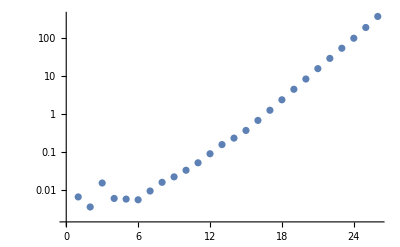

```mathematica
ListLogPlot[times]
```

```mathematica
(*ISU3L25=tmp;
Save[NotebookDirectory[]<>"index.m",{ISU3L25,index}];*)
```

```mathematica
(*Load[NotebookDirectory[]<>"index.m"];
tmp=ISU3L25;*)
```

#### Without Simplify

```mathematica
NN=3;
LL=30;
Timing[tmp=Sum[index[NN,L],{L,0,LL}]][[1]]
```

396.912

#### Analysis

```mathematica
tmp/.ξ->1
```

1+3 t^2+4 t^4+7 t^6+6 t^8+12 t^10+8 t^12+15 t^14+13 t^16+18 t^18+12 t^20+28 t^22+14 t^24+O[t]^26

```mathematica
tmp/.ξ->ⅈ
```

1-t^2+4 t^4-t^6+6 t^8-4 t^10+8 t^12-t^14+13 t^16-6 t^18+12 t^20-4 t^22+14 t^24+O[t]^26

```mathematica
coefs=Total[Abs[CoefficientList[If[#=!=0,ξ^Exponent[#,ξ]*#,0],ξ]]]&/@Expand[CoefficientList[tmp,t]];
coefs.Table[t^n,{n,0,Length[coefs]-1}]
```

1+3 t^2+4 t^3+4 t^4+8 t^5+11 t^6+16 t^7+22 t^8+32 t^9+40 t^10+64 t^11+88 t^12+120 t^13+163 t^14+228 t^15+309 t^16+420 t^17+562 t^18+748 t^19+992 t^20+1312 t^21+1712 t^22+2256 t^23+2934 t^24+3808 t^25

```mathematica
coefs=Max[Table[Abs[#/.ξ->N[Exp[2π ⅈ n/1000],10]],{n,1,1000}]]&/@Expand[CoefficientList[tmp,t]]
```

{1,0,3.,3.07920075,4.,5.9489018,10.149181,9.38045,18.359707,24.597272,28.,49.756374,70.176866,86.669988,130.77542,178.29695,235.55924,329.79527,444.5547,578.71734,783.51952,1030.6788,1342.2813,1775.6366,2308.2967,2982.2442}

### flavored MacDonald index

```mathematica
Clear["Global`*"];

(* product of chracters *)
characterProduct[NN_,a_]:=characterProduct[NN,a]=Product[(Sum[w[i]^n/w[j]^n,{i,1,NN},{j,1,NN}]-1)^a[[n]],{n,1,Length[a]}]

(* generate a vector "a" with Sum[i a[[i]],{i,1,NN}] fixed to be L *)
power[NN_,a_]:=power[NN,a]=2 NN-2+2 Sum[i a[[i]],{i,1,Length[a]}]
aVectors[L_]:=aVectors[L]=Module[{partition,vector},
partition=IntegerPartitions[L];
vector[n_]:=Sum[Table[KroneckerDelta[n[[j]],i],{i,1,L}],{j,1,Length[n]}];
Table[vector[partition[[i]]],{i,1,Length[partition]}]
]


coefficient[a_]:=coefficient[a]=Product[1/a[[i]]!/(i^(a[[i]])),{i,1,Length[a]}]

f[x_,b_,s_]:=1-((1-b s x)(1-b^-1 s x))/(1-x^2)

groupIntegrand[NN_,a_]:=groupIntegrand[NN,a]=characterProduct[NN,a](*Product[1/w[i],{i,1,NN-1}]*)(-1)^(NN(NN-1)/2)(*/Product[w[i]^(NN-1),{i,1,NN}]*)Product[(w[i]-w[j])^2,{i,1,NN},{j,1,i-1}]/.w[NN]->1/Product[w[i],{i,1,NN-1}]

Clear[groupIntegrandNumerator,groupIntegral,index]
groupIntegrandNumerator[NN_,a_]:=groupIntegrandNumerator[NN,a]=Numerator[groupIntegrand[NN,a]//Together]

groupIntegral[NN_,a_]:=groupIntegral[NN,a]=1/NN!Coefficient[ groupIntegrandNumerator[NN,a]//Expand,Product[w[i],{i,1,NN-1}]^power[NN,a] ]

index[NN_,L_]:=index[NN,L]=Module[{as},
as=aVectors[L];
Sum[Product[f[x^j,b^j,s^j]^as[[i,j]],{j,1,L}]groupIntegral[NN,as[[i]]]coefficient[as[[i]]],{i,1,Length[as]}]
]
```

```mathematica
NN=2;
LL=24;
AbsoluteTiming[tmp=Sum[index[NN,L],{L,0,LL}]+O[x]^(LL+1)//Simplify]
```

{213.562,1+((1+b^2+b^4) s^2 x^2)/b^2-((1+b^2) s (1+s^2) x^3)/b+(s^2 (s^2+b^8 s^2+b^2 (1+s^2)+b^6 (1+s^2)+b^4 (2+s^2)) x^4)/b^4-((1+b^2) s (1+s^2) (b^2+s^2+b^4 s^2) x^5)/b^3+(s^2 (s^4+b^12 s^4+b^2 (s^2+s^4)+b^10 (s^2+s^4)+b^4 (1+3 s^2+s^4)+b^8 (1+3 s^2+s^4)+b^6 (2+3 s^2+s^4)) x^6)/b^6-((1+b^2) s (1+s^2) (2 b^2 s^2+2 b^6 s^2+s^4+b^8 s^4+b^4 (1+s^2+s^4)) x^7)/b^5+(s^2 (s^6+b^16 s^6+b^4 s^2 (2+3 s^2+s^4)+b^12 s^2 (2+3 s^2+s^4)+b^2 (s^4+s^6)+b^14 (s^4+s^6)+b^6 (2+6 s^2+4 s^4+s^6)+b^10 (2+6 s^2+4 s^4+s^6)+b^8 (3+8 s^2+4 s^4+s^6)) x^8)/b^8-((1+b^2) s (1+s^2) (2 b^2 s^4+2 b^10 s^4+s^6+b^12 s^6+b^4 s^2 (3+s^2+s^4)+b^8 s^2 (3+s^2+s^4)+b^6 (1+3 s^2+2 s^4)) x^9)/b^7+1/b^10 s^2 (s^8+b^20 s^8+b^4 s^4 (2+3 s^2+s^4)+b^16 s^4 (2+3 s^2+s^4)+b^6 s^2 (3+7 s^2+4 s^4+s^6)+b^14 s^2 (3+7 s^2+4 s^4+s^6)+b^2 (s^6+s^8)+b^18 (s^6+s^8)+b^8 (2+10 s^2+10 s^4+4 s^6+s^8)+b^12 (2+10 s^2+10 s^4+4 s^6+s^8)+b^10 (4+13 s^2+11 s^4+4 s^6+s^8)) x^10-((1+b^2) s (1+s^2) (2 b^2 s^6+2 b^14 s^6+s^8+b^16 s^8+b^4 s^4 (4+s^2+s^4)+b^12 s^4 (4+s^2+s^4)+2 b^6 s^2 (2+2 s^2+s^4)+2 b^10 s^2 (2+2 s^2+s^4)+b^8 (1+5 s^2+5 s^4+s^6+s^8)) x^11)/b^9+1/b^12 s^2 (s^10+b^24 s^10+b^4 s^6 (2+3 s^2+s^4)+b^20 s^6 (2+3 s^2+s^4)+b^6 s^4 (4+7 s^2+4 s^4+s^6)+b^18 s^4 (4+7 s^2+4 s^4+s^6)+b^8 s^2 (5+14 s^2+11 s^4+4 s^6+s^8)+b^16 s^2 (5+14 s^2+11 s^4+4 s^6+s^8)+b^2 (s^8+s^10)+b^22 (s^8+s^10)+b^10 (3+15 s^2+22 s^4+12 s^6+4 s^8+s^10)+b^14 (3+15 s^2+22 s^4+12 s^6+4 s^8+s^10)+b^12 (5+21 s^2+25 s^4+12 s^6+4 s^8+s^10)) x^12-1/b^11(1+b^2) s (1+s^2) (2 b^2 s^8+2 b^18 s^8+s^10+b^20 s^10+b^4 s^6 (4+s^2+s^4)+b^16 s^6 (4+s^2+s^4)+2 b^6 s^4 (3+2 s^2+s^4)+2 b^14 s^4 (3+2 s^2+s^4)+b^8 s^2 (5+9 s^2+5 s^4+s^6+s^8)+b^12 s^2 (5+9 s^2+5 s^4+s^6+s^8)+b^10 (1+7 s^2+10 s^4+4 s^6+2 s^8)) x^13+1/b^14 s^2 (s^12+b^28 s^12+b^4 s^8 (2+3 s^2+s^4)+b^24 s^8 (2+3 s^2+s^4)+b^6 s^6 (4+7 s^2+4 s^4+s^6)+b^22 s^6 (4+7 s^2+4 s^4+s^6)+b^8 s^4 (6+15 s^2+11 s^4+4 s^6+s^8)+b^20 s^4 (6+15 s^2+11 s^4+4 s^6+s^8)+b^10 s^2 (7+24 s^2+25 s^4+12 s^6+4 s^8+s^10)+b^18 s^2 (7+24 s^2+25 s^4+12 s^6+4 s^8+s^10)+b^2 (s^10+s^12)+b^26 (s^10+s^12)+b^12 (3+22 s^2+41 s^4+30 s^6+12 s^8+4 s^10+s^12)+b^16 (3+22 s^2+41 s^4+30 s^6+12 s^8+4 s^10+s^12)+b^14 (6+30 s^2+47 s^4+31 s^6+12 s^8+4 s^10+s^12)) x^14-1/b^13(1+b^2) s (1+s^2) (2 b^2 s^10+2 b^22 s^10+s^12+b^24 s^12+b^4 s^8 (4+s^2+s^4)+b^20 s^8 (4+s^2+s^4)+b^6 s^6 (7+4 s^2+2 s^4)+b^18 s^6 (7+4 s^2+2 s^4)+b^8 s^4 (9+10 s^2+5 s^4+s^6+s^8)+b^16 s^4 (9+10 s^2+5 s^4+s^6+s^8)+b^10 s^2 (7+16 s^2+12 s^4+4 s^6+2 s^8)+b^14 s^2 (7+16 s^2+12 s^4+4 s^6+2 s^8)+b^12 (1+9 s^2+19 s^4+11 s^6+5 s^8+s^10+s^12)) x^15+1/b^16 s^2 (s^14+b^32 s^14+b^4 s^10 (2+3 s^2+s^4)+b^28 s^10 (2+3 s^2+s^4)+b^6 s^8 (4+7 s^2+4 s^4+s^6)+b^26 s^8 (4+7 s^2+4 s^4+s^6)+b^8 s^6 (7+15 s^2+11 s^4+4 s^6+s^8)+b^24 s^6 (7+15 s^2+11 s^4+4 s^6+s^8)+b^10 s^4 (10+28 s^2+26 s^4+12 s^6+4 s^8+s^10)+b^22 s^4 (10+28 s^2+26 s^4+12 s^6+4 s^8+s^10)+b^12 s^2 (10+39 s^2+51 s^4+31 s^6+12 s^8+4 s^10+s^12)+b^20 s^2 (10+39 s^2+51 s^4+31 s^6+12 s^8+4 s^10+s^12)+b^2 (s^12+s^14)+b^30 (s^12+s^14)+b^14 (4+31 s^2+70 s^4+64 s^6+32 s^8+12 s^10+4 s^12+s^14)+b^18 (4+31 s^2+70 s^4+64 s^6+32 s^8+12 s^10+4 s^12+s^14)+b^16 (7+43 s^2+82 s^4+68 s^6+32 s^8+12 s^10+4 s^12+s^14)) x^16-1/b^15(1+b^2) s (1+s^2) (2 b^2 s^12+2 b^26 s^12+s^14+b^28 s^14+b^4 s^10 (4+s^2+s^4)+b^24 s^10 (4+s^2+s^4)+b^6 s^8 (7+4 s^2+2 s^4)+b^22 s^8 (7+4 s^2+2 s^4)+b^8 s^6 (11+10 s^2+5 s^4+s^6+s^8)+b^20 s^6 (11+10 s^2+5 s^4+s^6+s^8)+b^10 s^4 (13+20 s^2+12 s^4+4 s^6+2 s^8)+b^18 s^4 (13+20 s^2+12 s^4+4 s^6+2 s^8)+b^12 s^2 (8+26 s^2+24 s^4+11 s^6+5 s^8+s^10+s^12)+b^16 s^2 (8+26 s^2+24 s^4+11 s^6+5 s^8+s^10+s^12)+b^14 (1+12 s^2+31 s^4+25 s^6+12 s^8+4 s^10+2 s^12)) x^17+1/b^18 s^2 (s^16+b^36 s^16+b^4 s^12 (2+3 s^2+s^4)+b^32 s^12 (2+3 s^2+s^4)+b^6 s^10 (4+7 s^2+4 s^4+s^6)+b^30 s^10 (4+7 s^2+4 s^4+s^6)+b^8 s^8 (7+15 s^2+11 s^4+4 s^6+s^8)+b^28 s^8 (7+15 s^2+11 s^4+4 s^6+s^8)+b^10 s^6 (11+29 s^2+26 s^4+12 s^6+4 s^8+s^10)+b^26 s^6 (11+29 s^2+26 s^4+12 s^6+4 s^8+s^10)+b^12 s^4 (15+48 s^2+54 s^4+31 s^6+12 s^8+4 s^10+s^12)+b^24 s^4 (15+48 s^2+54 s^4+31 s^6+12 s^8+4 s^10+s^12)+b^14 s^2 (13+60 s^2+93 s^4+69 s^6+32 s^8+12 s^10+4 s^12+s^14)+b^22 s^2 (13+60 s^2+93 s^4+69 s^6+32 s^8+12 s^10+4 s^12+s^14)+b^2 (s^14+s^16)+b^34 (s^14+s^16)+b^16 (4+42 s^2+111 s^4+123 s^6+74 s^8+32 s^10+12 s^12+4 s^14+s^16)+b^20 (4+42 s^2+111 s^4+123 s^6+74 s^8+32 s^10+12 s^12+4 s^14+s^16)+b^18 (8+58 s^2+133 s^4+132 s^6+75 s^8+32 s^10+12 s^12+4 s^14+s^16)) x^18-1/b^17(1+b^2) s (1+s^2) (2 b^2 s^14+2 b^30 s^14+s^16+b^32 s^16+b^4 s^12 (4+s^2+s^4)+b^28 s^12 (4+s^2+s^4)+b^6 s^10 (7+4 s^2+2 s^4)+b^26 s^10 (7+4 s^2+2 s^4)+b^8 s^8 (12+10 s^2+5 s^4+s^6+s^8)+b^24 s^8 (12+10 s^2+5 s^4+s^6+s^8)+b^10 s^6 (17+21 s^2+12 s^4+4 s^6+2 s^8)+b^22 s^6 (17+21 s^2+12 s^4+4 s^6+2 s^8)+b^12 s^4 (18+36 s^2+26 s^4+11 s^6+5 s^8+s^10+s^12)+b^20 s^4 (18+36 s^2+26 s^4+11 s^6+5 s^8+s^10+s^12)+b^14 s^2 (10+39 s^2+46 s^4+26 s^6+12 s^8+4 s^10+2 s^12)+b^18 s^2 (10+39 s^2+46 s^4+26 s^6+12 s^8+4 s^10+2 s^12)+b^16 (1+15 s^2+48 s^4+49 s^6+27 s^8+11 s^10+5 s^12+s^14+s^16)) x^19+1/b^20 s^2 (s^18+b^40 s^18+b^4 s^14 (2+3 s^2+s^4)+b^36 s^14 (2+3 s^2+s^4)+b^6 s^12 (4+7 s^2+4 s^4+s^6)+b^34 s^12 (4+7 s^2+4 s^4+s^6)+b^8 s^10 (7+15 s^2+11 s^4+4 s^6+s^8)+b^32 s^10 (7+15 s^2+11 s^4+4 s^6+s^8)+b^10 s^8 (12+29 s^2+26 s^4+12 s^6+4 s^8+s^10)+b^30 s^8 (12+29 s^2+26 s^4+12 s^6+4 s^8+s^10)+b^12 s^6 (18+52 s^2+55 s^4+31 s^6+12 s^8+4 s^10+s^12)+b^28 s^6 (18+52 s^2+55 s^4+31 s^6+12 s^8+4 s^10+s^12)+b^14 s^4 (22+79 s^2+104 s^4+70 s^6+32 s^8+12 s^10+4 s^12+s^14)+b^26 s^4 (22+79 s^2+104 s^4+70 s^6+32 s^8+12 s^10+4 s^12+s^14)+b^16 s^2 (17+89 s^2+162 s^4+140 s^6+75 s^8+32 s^10+12 s^12+4 s^14+s^16)+b^24 s^2 (17+89 s^2+162 s^4+140 s^6+75 s^8+32 s^10+12 s^12+4 s^14+s^16)+b^2 (s^16+s^18)+b^38 (s^16+s^18)+b^18 (5+55 s^2+169 s^4+221 s^6+156 s^8+76 s^10+32 s^12+12 s^14+4 s^16+s^18)+b^22 (5+55 s^2+169 s^4+221 s^6+156 s^8+76 s^10+32 s^12+12 s^14+4 s^16+s^18)+b^20 (9+77 s^2+203 s^4+241 s^6+160 s^8+76 s^10+32 s^12+12 s^14+4 s^16+s^18)) x^20-1/b^19(1+b^2) s (1+s^2) (2 b^2 s^16+2 b^34 s^16+s^18+b^36 s^18+b^4 s^14 (4+s^2+s^4)+b^32 s^14 (4+s^2+s^4)+b^6 s^12 (7+4 s^2+2 s^4)+b^30 s^12 (7+4 s^2+2 s^4)+b^8 s^10 (12+10 s^2+5 s^4+s^6+s^8)+b^28 s^10 (12+10 s^2+5 s^4+s^6+s^8)+b^10 s^8 (19+21 s^2+12 s^4+4 s^6+2 s^8)+b^26 s^8 (19+21 s^2+12 s^4+4 s^6+2 s^8)+b^12 s^6 (25+40 s^2+26 s^4+11 s^6+5 s^8+s^10+s^12)+b^24 s^6 (25+40 s^2+26 s^4+11 s^6+5 s^8+s^10+s^12)+b^14 s^4 (24+60 s^2+51 s^4+26 s^6+12 s^8+4 s^10+2 s^12)+b^22 s^4 (24+60 s^2+51 s^4+26 s^6+12 s^8+4 s^10+2 s^12)+b^16 s^2 (12+55 s^2+81 s^4+55 s^6+27 s^8+11 s^10+5 s^12+s^14+s^16)+b^20 s^2 (12+55 s^2+81 s^4+55 s^6+27 s^8+11 s^10+5 s^12+s^14+s^16)+b^18 (1+18 s^2+70 s^4+88 s^6+56 s^8+26 s^10+12 s^12+4 s^14+2 s^16)) x^21+1/b^22 s^2 (s^20+b^44 s^20+b^4 s^16 (2+3 s^2+s^4)+b^40 s^16 (2+3 s^2+s^4)+b^6 s^14 (4+7 s^2+4 s^4+s^6)+b^38 s^14 (4+7 s^2+4 s^4+s^6)+b^8 s^12 (7+15 s^2+11 s^4+4 s^6+s^8)+b^36 s^12 (7+15 s^2+11 s^4+4 s^6+s^8)+b^10 s^10 (12+29 s^2+26 s^4+12 s^6+4 s^8+s^10)+b^34 s^10 (12+29 s^2+26 s^4+12 s^6+4 s^8+s^10)+b^12 s^8 (19+53 s^2+55 s^4+31 s^6+12 s^8+4 s^10+s^12)+b^32 s^8 (19+53 s^2+55 s^4+31 s^6+12 s^8+4 s^10+s^12)+b^14 s^6 (27+88 s^2+107 s^4+70 s^6+32 s^8+12 s^10+4 s^12+s^14)+b^30 s^6 (27+88 s^2+107 s^4+70 s^6+32 s^8+12 s^10+4 s^12+s^14)+b^16 s^4 (30+124 s^2+186 s^4+145 s^6+75 s^8+32 s^10+12 s^12+4 s^14+s^16)+b^28 s^4 (30+124 s^2+186 s^4+145 s^6+75 s^8+32 s^10+12 s^12+4 s^14+s^16)+b^18 s^2 (21+127 s^2+263 s^4+264 s^6+161 s^8+76 s^10+32 s^12+12 s^14+4 s^16+s^18)+b^26 s^2 (21+127 s^2+263 s^4+264 s^6+161 s^8+76 s^10+32 s^12+12 s^14+4 s^16+s^18)+b^2 (s^18+s^20)+b^42 (s^18+s^20)+b^20 (5+70 s^2+245 s^4+372 s^6+303 s^8+166 s^10+76 s^12+32 s^14+12 s^16+4 s^18+s^20)+b^24 (5+70 s^2+245 s^4+372 s^6+303 s^8+166 s^10+76 s^12+32 s^14+12 s^16+4 s^18+s^20)+b^22 (10+98 s^2+298 s^4+410 s^6+314 s^8+167 s^10+76 s^12+32 s^14+12 s^16+4 s^18+s^20)) x^22-1/b^21(1+b^2) s (1+s^2) (2 b^2 s^18+2 b^38 s^18+s^20+b^40 s^20+b^4 s^16 (4+s^2+s^4)+b^36 s^16 (4+s^2+s^4)+b^6 s^14 (7+4 s^2+2 s^4)+b^34 s^14 (7+4 s^2+2 s^4)+b^8 s^12 (12+10 s^2+5 s^4+s^6+s^8)+b^32 s^12 (12+10 s^2+5 s^4+s^6+s^8)+b^10 s^10 (20+21 s^2+12 s^4+4 s^6+2 s^8)+b^30 s^10 (20+21 s^2+12 s^4+4 s^6+2 s^8)+b^12 s^8 (29+41 s^2+26 s^4+11 s^6+5 s^8+s^10+s^12)+b^28 s^8 (29+41 s^2+26 s^4+11 s^6+5 s^8+s^10+s^12)+b^14 s^6 (36+70 s^2+53 s^4+26 s^6+12 s^8+4 s^10+2 s^12)+b^26 s^6 (36+70 s^2+53 s^4+26 s^6+12 s^8+4 s^10+2 s^12)+b^16 s^4 (32+93 s^2+96 s^4+56 s^6+27 s^8+11 s^10+5 s^12+s^14+s^16)+b^24 s^4 (32+93 s^2+96 s^4+56 s^6+27 s^8+11 s^10+5 s^12+s^14+s^16)+b^18 s^2 (14+76 s^2+134 s^4+107 s^6+58 s^8+26 s^10+12 s^12+4 s^14+2 s^16)+b^22 s^2 (14+76 s^2+134 s^4+107 s^6+58 s^8+26 s^10+12 s^12+4 s^14+2 s^16)+b^20 (1+22 s^2+98 s^4+147 s^6+110 s^8+57 s^10+27 s^12+11 s^14+5 s^16+s^18+s^20)) x^23+1/b^24 s^2 (s^22+b^48 s^22+b^4 s^18 (2+3 s^2+s^4)+b^44 s^18 (2+3 s^2+s^4)+b^6 s^16 (4+7 s^2+4 s^4+s^6)+b^42 s^16 (4+7 s^2+4 s^4+s^6)+b^8 s^14 (7+15 s^2+11 s^4+4 s^6+s^8)+b^40 s^14 (7+15 s^2+11 s^4+4 s^6+s^8)+b^10 s^12 (12+29 s^2+26 s^4+12 s^6+4 s^8+s^10)+b^38 s^12 (12+29 s^2+26 s^4+12 s^6+4 s^8+s^10)+b^12 s^10 (20+53 s^2+55 s^4+31 s^6+12 s^8+4 s^10+s^12)+b^36 s^10 (20+53 s^2+55 s^4+31 s^6+12 s^8+4 s^10+s^12)+b^14 s^8 (30+92 s^2+108 s^4+70 s^6+32 s^8+12 s^10+4 s^12+s^14)+b^34 s^8 (30+92 s^2+108 s^4+70 s^6+32 s^8+12 s^10+4 s^12+s^14)+b^16 s^6 (40+143 s^2+197 s^4+146 s^6+75 s^8+32 s^10+12 s^12+4 s^14+s^16)+b^32 s^6 (40+143 s^2+197 s^4+146 s^6+75 s^8+32 s^10+12 s^12+4 s^14+s^16)+b^18 s^4 (42+187 s^2+318 s^4+281 s^6+162 s^8+76 s^10+32 s^12+12 s^14+4 s^16+s^18)+b^30 s^4 (42+187 s^2+318 s^4+281 s^6+162 s^8+76 s^10+32 s^12+12 s^14+4 s^16+s^18)+b^20 s^2 (27+177 s^2+413 s^4+470 s^6+324 s^8+167 s^10+76 s^12+32 s^14+12 s^16+4 s^18+s^20)+b^28 s^2 (27+177 s^2+413 s^4+470 s^6+324 s^8+167 s^10+76 s^12+32 s^14+12 s^16+4 s^18+s^20)+b^2 (s^20+s^22)+b^46 (s^20+s^22)+b^22 (6+88 s^2+348 s^4+598 s^6+556 s^8+340 s^10+168 s^12+76 s^14+32 s^16+12 s^18+4 s^20+s^22)+b^26 (6+88 s^2+348 s^4+598 s^6+556 s^8+340 s^10+168 s^12+76 s^14+32 s^16+12 s^18+4 s^20+s^22)+b^24 (11+124 s^2+425 s^4+667 s^6+581 s^8+344 s^10+168 s^12+76 s^14+32 s^16+12 s^18+4 s^20+s^22)) x^24+O[x]^25}

### flavored Hall-Littlewood index

```mathematica
Clear["Global`*"];

(* product of chracters *)
characterProduct[NN_,a_]:=characterProduct[NN,a]=Product[(Sum[w[i]^n/w[j]^n,{i,1,NN},{j,1,NN}]-1)^a[[n]],{n,1,Length[a]}]

(* generate a vector "a" with Sum[i a[[i]],{i,1,NN}] fixed to be L *)
power[NN_,a_]:=power[NN,a]=2 NN-2+2 Sum[i a[[i]],{i,1,Length[a]}]
aVectors[L_]:=aVectors[L]=Module[{partition,vector},
partition=IntegerPartitions[L];
vector[n_]:=Sum[Table[KroneckerDelta[n[[j]],i],{i,1,L}],{j,1,Length[n]}];
Table[vector[partition[[i]]],{i,1,Length[partition]}]
]


coefficient[a_]:=coefficient[a]=Product[1/a[[i]]!/(i^(a[[i]])),{i,1,Length[a]}]

f[x_,b_]:=1-(1-b x)(1-b^-1 x)

groupIntegrand[NN_,a_]:=groupIntegrand[NN,a]=characterProduct[NN,a](*Product[1/w[i],{i,1,NN-1}]*)(-1)^(NN(NN-1)/2)(*/Product[w[i]^(NN-1),{i,1,NN}]*)Product[(w[i]-w[j])^2,{i,1,NN},{j,1,i-1}]/.w[NN]->1/Product[w[i],{i,1,NN-1}]

Clear[groupIntegrandNumerator,groupIntegral,index]
groupIntegrandNumerator[NN_,a_]:=groupIntegrandNumerator[NN,a]=Numerator[groupIntegrand[NN,a]//Together]

groupIntegral[NN_,a_]:=groupIntegral[NN,a]=1/NN!Coefficient[ groupIntegrandNumerator[NN,a]//Expand,Product[w[i],{i,1,NN-1}]^power[NN,a] ]

index[NN_,L_]:=index[NN,L]=Module[{as},
as=aVectors[L];
Sum[Product[f[x^j,b^j]^as[[i,j]],{j,1,L}]groupIntegral[NN,as[[i]]]coefficient[as[[i]]],{i,1,Length[as]}]
]
```

```mathematica
NN=3;
LL=18;
AbsoluteTiming[tmp=Sum[index[NN,L],{L,0,LL}]+O[x]^(LL+1)//Simplify]
```

{7.2715,1+(1+1/b^2+b^2) x^2+(1/b^3+b^3) x^3+(1+1/b^4+b^4) x^4+(1/b^5+1/b^3+b^3+b^5) x^5+(1+2/b^6+2 b^6) x^6+(1/b^7+1/b^3+b^3+b^7) x^7+(1+2/b^8+1/b^6+b^6+2 b^8) x^8+(2/b^9+1/b^3+b^3+2 b^9) x^9+(1+2/b^10+1/b^6+b^6+2 b^10) x^10+((2+b^2+b^8+b^14+b^20+2 b^22) x^11)/b^11+(1+3/b^12+1/b^6+b^6+3 b^12) x^12+(2/b^13+1/b^9+1/b^3+b^3+b^9+2 b^13) x^13+(1+3/b^14+1/b^12+1/b^6+b^6+b^12+3 b^14) x^14+(3/b^15+1/b^9+1/b^3+b^3+b^9+3 b^15) x^15+(1+3/b^16+1/b^12+1/b^6+b^6+b^12+3 b^16) x^16+((3+b^2+b^8+b^14+b^20+b^26+b^32+3 b^34) x^17)/b^17+(1+4/b^18+1/b^12+1/b^6+b^6+b^12+4 b^18) x^18+O[x]^19}

### TODO: Hatsuda-Okazaki

```mathematica
cut=3;
exp=Sum[Log[1-μ ξ^-p/(1-u (q+O[q]^cut)^p)],{p,-cut,cut}]//Simplify
```

(Log[(-1+u+μ)/(-1+u)]+Log[1-μ/ξ^3]+Log[1-μ/ξ^2]+Log[1-μ/ξ])+((u μ)/(μ-ξ)+(μ ξ)/u) q+(μ ((u^4 (μ-2 ξ))/(μ-ξ)^2+2 u ξ^2+ξ (2-μ ξ)+(2 u^3)/(μ-ξ^2)) q^2)/(2 u^2)+O[q]^3

```mathematica
cut=3;
exp=Sum[Log[1-μ ξ^-p/(1-u (q+O[q]^cut)^p)],{p,-cut,cut}]//Simplify
```

### TODO: faster flavored Schur index

```mathematica
indexNumξ[LL_,L_,ξ_]:=indexNumξ[LL,L,ξ]=Module[{as},
as=aVectors[L];
Sum[Product[Series[f[t^j,ξ^j],{t,0,LL}]^as[[i,j]],{j,1,L}]groupIntegral[NN,as[[i]]]coefficient[as[[i]]],{i,1,Length[as]}]
]
```

```mathematica
NN=3;
LL=30;
Chop[Series[Sum[indexNumξ[LL,L,-1],{L,0,LL}],{t,0,LL}]]
```

## GAP

### 1/16 unrefined index

```mathematica
Clear[SnChar];
SnChar[n_,NN_]:=SnChar[n,NN]=Module[{fn=NotebookDirectory[]<>"sn/"<>ToString[n]<>"_"<>ToString[NN]<>".m"},
If[FileExistsQ[fn],
Get[fn],
Print["Missing n="<>ToString[n]<>" N="<>ToString[NN]];
]
];
```

```mathematica
z[P_]:=(Times@@P)Product[i[[2]]!,{i,Tally[P]}];
is[x_]:=1-((1-x^2)^3)/((1-x^3)^2);
indexGAP[N_,level_]:=Module[{snchar},
snchar=SnChar[level,N];
Sum[
Product[is[x^i],{i,P[[1]]}] 1/z[P[[1]]]
P[[2]]
,{P,snchar}]
];
```

```mathematica
n=30;
AbsoluteTiming[Series[(1+Sum[indexGAP[2,i],{i,1,n}])/(1+Sum[indexGAP[1,i],{i,1,n}]),{x,0,n}]]
```

{8.01475,1+6 x^4-6 x^5-7 x^6+18 x^7+6 x^8-36 x^9+6 x^10+84 x^11-80 x^12-132 x^13+309 x^14-18 x^15-567 x^16+516 x^17+613 x^18-1392 x^19-180 x^20+2884 x^21-1926 x^22-4242 x^23+7890 x^24+792 x^25-15876 x^26+13804 x^27+15177 x^28-37536 x^29+7049 x^30+O[x]^31}

```mathematica
n=30;
AbsoluteTiming[Series[(1+Sum[indexGAP[3,i],{i,1,n}])/(1+Sum[indexGAP[1,i],{i,1,n}]),{x,0,n}]]
```

{7.97039,1+6 x^4-6 x^5+3 x^6+6 x^7-16 x^9+27 x^10+18 x^11-87 x^12+96 x^13+54 x^14-222 x^15+132 x^16+210 x^17-235 x^18-468 x^19+1284 x^20-534 x^21-2268 x^22+4392 x^23-1995 x^24-4128 x^25+6957 x^26-1288 x^27-5310 x^28-2376 x^29+22695 x^30+O[x]^31}

### unflavored Schur index

```mathematica
Clear[SnChar];
SnChar[n_,NN_]:=SnChar[n,NN]=Module[{fn=NotebookDirectory[]<>"sn/"<>ToString[n]<>"_"<>ToString[NN]<>".m"},
If[FileExistsQ[fn],
Get[fn],
Print["Missing n="<>ToString[n]<>" N="<>ToString[NN]];
]
];
```

```mathematica
z[P_]:=(Times@@P)Product[i[[2]]!,{i,Tally[P]}];
is[x_]:=1-(1-x)^2/(1-x^2);
indexGAP[N_,level_]:=Module[{snchar},
snchar=SnChar[level,N];
Sum[
Product[is[x^i],{i,P[[1]]}] 1/z[P[[1]]]
P[[2]]
,{P,snchar}]
];
```

```mathematica
n=15;
Series[(1+Sum[indexGAP[2,i],{i,1,n}])/(1+Sum[indexGAP[1,i],{i,1,n}]),{x,0,n}]
```

1+3 x^2-4 x^3+9 x^4-12 x^5+22 x^6-36 x^7+60 x^8-88 x^9+135 x^10-204 x^11+302 x^12-432 x^13+627 x^14-900 x^15+O[x]^16

### flavored Schur index

```mathematica
Clear["Global`*"];
SnChar[n_,NN_]:=SnChar[n,NN]=Module[{fn=NotebookDirectory[]<>"sn/"<>ToString[n]<>"_"<>ToString[NN]<>".m"},
If[FileExistsQ[fn],
Get[fn],
Print["Missing n="<>ToString[n]<>" N="<>ToString[NN]];
]
];
```

```mathematica
z[P_]:=(Times@@P)Product[i[[2]]!,{i,Tally[P]}];
is[x_,b_]:=1-((1-b x)(1-b^-1 x))/(1-x^2);
indexGAP[N_,level_]:=Module[{snchar},
snchar=SnChar[level,N];
Sum[
Product[is[x^i,b^i],{i,P[[1]]}] 1/z[P[[1]]]
P[[2]]
,{P,snchar}]
];
```

```mathematica
n=15;
tmp=Series[(1+Sum[indexGAP[3,i],{i,1,n}])/(1+Sum[indexGAP[1,i],{i,1,n}]),{x,0,n}];
tmp=Sum[Expand[SeriesCoefficient[tmp,{x,0,i}]]x^i,{i,0,n}]+O[x]^(n+1);
```

```mathematica
coefs=Total[Abs[CoefficientList[If[#=!=0,ξ^Exponent[#,ξ]*#,0],ξ]]]&/@Expand[CoefficientList[tmp,x]];
coefs.Table[x^n,{n,0,Length[coefs]-1}]
```

1+3 x^2+4 x^3+4 x^4+8 x^5+11 x^6+16 x^7+22 x^8+32 x^9+40 x^10+64 x^11+88 x^12+120 x^13+163 x^14+228 x^15

```mathematica
NN=3;
Monitor[times=Table[AbsoluteTiming[
tmp=Series[(1+Sum[indexGAP[NN,i],{i,1,n}])/(1+Sum[indexGAP[1,i],{i,1,n}]),{x,0,n}];
tmp=Sum[Expand[SeriesCoefficient[tmp,{x,0,i}]]x^i,{i,0,n}]+O[x]^(n+1);][[1]],{n,0,20}];
,n]
```

```mathematica
times
```

{0.000385,0.005231,0.003296,0.004997,0.015982,0.011472,0.009223,0.009586,0.018855,0.036239,0.082976,0.278406,0.501553,0.916047,1.64093,2.93195,5.39749,8.54385,18.6088,36.0703,63.858}

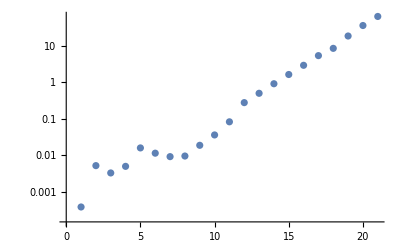

```mathematica
ListLogPlot[times]
```

### Junk

```mathematica
(*SnChar[n_,NN_]:=Module[{},
script="LoadPackage( \"ctbllib\" );;
	SnChar := function(n, N)
	\tlocal ct, irr, cp, short, part, sq, ans;
	\tct := CharacterTable(\"Symmetric\", n);;
	\tirr := Irr(ct);;
	\tcp := ClassParameters(ct);;
	\tshort := Filtered([1..Length(cp)], x->Length(cp[x][2]) <= N);;
	\tpart := List(cp, x -> x[2]);;
	\tsq := Sum(short, x -> irr[x] * irr[x]);;
	\tans := List([1..Length(part)], x -> [part[x], sq[x]]);;
	\tPrintTo(\"/Users/yinhslin/Downloads/index/output.txt\", ans);;
	end;;";
	script=script<>"
	SnChar("<>ToString[n]<>","<>ToString[NN]<>");;";

Export[NotebookDirectory[]<>"sym.txt",script];
DeleteFile[NotebookDirectory[]<>"sym.g"];
RenameFile[NotebookDirectory[]<>"sym.txt",NotebookDirectory[]<>"sym.g"];
gap="/Users/yinhslin/Downloads/gap-4.12.2/gap";
Run[gap<>" -q < "<>NotebookDirectory[]<>"sym.g"];

output=Import[NotebookDirectory[]<>"output.txt"];
output=StringReplace[output,{"["->"{","]"->"}"}]//ToExpression;
output
];*)
```

## GroupMath

```mathematica
<<GroupMath`
```

paclet:GroupMath/tutorial/GroupMathDoc | XXXXXXXXXXXXXXXXXXXXXXXXXXX GroupMath XXXXXXXXXXXXXXXXXXXXXXXXXXVersion: 1.1.2 (6/May/2020)Author: Renato FonsecaReference: 2011.01764 [hep-th]Website: http://renatofonseca.net/groupmathBuilt-in documentation: paclet:GroupMath/tutorial/GroupMathDocXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXX

SetDelayed::write: Tag BlockDiagonalMatrix in BlockDiagonalMatrix[blocks_] is Protected.

### Sn characters complexity analysis

```mathematica
partitions=IntegerPartitions[30];
shortPartitions=Select[partitions,Length[#]<=5&];
```

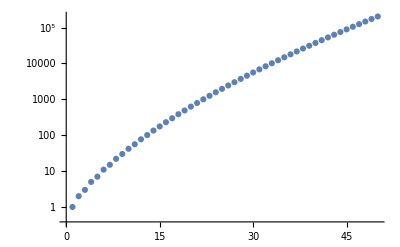

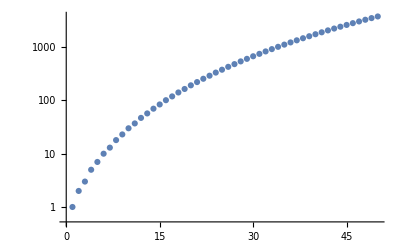

```mathematica
ListLogPlot[Table[Length[IntegerPartitions[n]],{n,1,50}]]
ListLogPlot[Table[Length[Select[IntegerPartitions[n],Length[#]<=5&]],{n,1,50}]]
```

### 1/16 unrefined index

```mathematica
z[P_]:=(Times@@P)Product[i[[2]]!,{i,Tally[P]}]
is[x_]:=1-((1-x^2)^3)/((1-x^3)^2)
index[N_,level_]:=Module[{partitions,shortPartitions},
partitions=IntegerPartitions[level];
shortPartitions=Select[partitions,Length[#]<=N&];
Sum[
Product[is[x^i],{i,P}] 1/z[P]
SnClassCharacter[λ,P]^2
,{λ,shortPartitions},{P,partitions}]
]
```

```mathematica
n=18;
Series[Sum[index[2,i],{i,1,n}],{x,0,2n+1}]
```

3 x^2-2 x^3+9 x^4-6 x^5+11 x^6-6 x^7+9 x^8+14 x^9-21 x^10+36 x^11-17 x^12-18 x^13+114 x^14-194 x^15+258 x^16-168 x^17-112 x^18+630 x^19-1089 x^20+1130 x^21-273 x^22-1632 x^23+4104 x^24-5364 x^25+3426 x^26+3152 x^27-13233 x^28+21336 x^29-18319 x^30-2994 x^31+40752 x^32-76884 x^33+78012 x^34-11808 x^35-121384 x^36+262206 x^37+O[x]^38

```mathematica
n=18;
Series[Sum[index[3,i],{i,1,n}],{x,0,2n+1}]
```

3 x^2-2 x^3+9 x^4-6 x^5+21 x^6-18 x^7+33 x^8-22 x^9+36 x^10+6 x^11-19 x^12+90 x^13-99 x^14+138 x^15-9 x^16-210 x^17+672 x^18-1116 x^19+1554 x^20-1270 x^21-36 x^22+2898 x^23-6705 x^24+10224 x^25-9918 x^26+2018 x^27+16470 x^28-42918 x^29+66906 x^30-66006 x^31+13566 x^32+106404 x^33-273204 x^34+407442 x^35-364710 x^36-12024 x^37+O[x]^38

### unflavored Schur index

```mathematica
z[P_]:=(Times@@P)Product[i[[2]]!,{i,Tally[P]}]
is[x_]:=1-(1-x)^2/(1-x^2)
index[N_,level_]:=Module[{partitions,shortPartitions},
partitions=IntegerPartitions[level];
shortPartitions=Select[partitions,Length[#]<=N&];
Sum[
Product[is[x^i],{i,P}] 1/z[P]
SnClassCharacter[λ,P]^2
,{λ,shortPartitions},{P,partitions}]
]
```

```mathematica
n=16;
Series[(1+Sum[index[2,i],{i,1,n}])/(1+Sum[index[1,i],{i,1,n}]),{x,0,n}]
```

1+3 x^2-4 x^3+9 x^4-12 x^5+22 x^6-36 x^7+60 x^8-88 x^9+135 x^10-204 x^11+302 x^12-432 x^13+627 x^14-900 x^15+1269 x^16+O[x]^17

```mathematica
n=10;
Series[(1+Sum[index[7,i],{i,1,n}])/(1+Sum[index[1,i],{i,1,n}]),{x,0,n}]
```

1+3 x^2+9 x^4+22 x^6+42 x^8+81 x^10+O[x]^11

## Mathematica built in FiniteGroupData

```mathematica
z[P_]:=(Times@@P)Product[i[[2]]!,{i,Tally[P]}]
is[x_]:=1-((1-x^2)^3)/((1-x^3)^2)
index[N_,level_]:=Module[{partitions,shortPartitions},
partitions=IntegerPartitions[level];
shortPartitions=Select[partitions,Length[#]<=N&];
Sum[
Product[is[x^i],{i,partitions[[k]]}] 1/z[partitions[[k]]]
FiniteGroupData[{"SymmetricGroup",level},"CharacterTable"][[j,Length[partitions]-k+1]]^2
,{j,1,Length[shortPartitions]},{k,1,Length[partitions]}]
]
```

```mathematica
Series[Sum[index[2,i],{i,1,10}],{x,0,12}]
```

3 x^2-2 x^3+9 x^4-6 x^5+11 x^6-6 x^7+9 x^8+14 x^9-21 x^10+36 x^11+81 x^12+O[x]^13

```mathematica
FiniteGroupData[{"SymmetricGroup",11},"CharacterTable"]
```

Missing[NotAvailable]

## Direct input

```mathematica
index[N_,level_]:=Module[{partitions,shortPartitions},
partitions=IntegerPartitions[level];
shortPartitions=Select[partitions,Length[#]<=N&];
Sum[
Product[is[x^i],{i,partitions[[k]]}] 1/z[partitions[[k]]]
χ[shortPartitions[[j]],partitions[[k]]]^2
,{j,1,Length[shortPartitions]},{k,1,Length[partitions]}]
]
 χ[{1},{1}]=1;
 χ[{1,1},{1,1}]=1;
 χ[{1,1},{2}]=-1;
 χ[{2},{1,1}]=1;
χ[{2},{2}]=1;
χ[{1,1,1},{1,1,1}]=1;
χ[{1,1,1},{2,1}]=-1;
χ[{1,1,1},{3}]=1;
χ[{2,1},{1,1,1}]=2;
χ[{2,1},{2,1}]=0;
χ[{2,1},{3}]=-1;
χ[{3},{1,1,1}]=1;
χ[{3},{2,1}]=1;
χ[{3},{3}]=1;
```